Cost of NVIDIA V100 Google Cloud per hour

```mathematica
2.28
```

2.28

training on 512 NVIDIA V100 GPU for 10 days

```mathematica
2.28 24 10 512
```

280166.

```mathematica
3.14 10^23/(7 10^12)/3600
```

1.24603×10^7

```mathematica
data=Import["C:\\Users\\ugo\\Desktop\\Daten contact\\Research\\KI\\NLP Models\\NLP_Models.xlsx"][[1]]
```

{{Model,Publication Date,Reference,Parameters,Training Dataset,Training Size,Training Size,Training Size GB,Remark},{Ulmfit,Thu 18 Jan 2018 00:00:00GMT+2,https://arxiv.org/abs/1801.06146,3.×10^6,Wikitext-103,30000.,1.×10^8,1 GB,First is articles, second words, third estimated (10 bytes per word)},{ELMO,Thu 15 Feb 2018 00:00:00GMT+2,https://allenai.org/allennlp/software/elmo,9.4×10^7,1 B Word Benchmark 
https://github.com/ciprian-chelba/1-billion-word-language-modeling-benchmark,,1.×10^9,10 GB,words, estimated size (10 bytes per word)},{BERT,Thu 11 Oct 2018 00:00:00GMT+2,https://arxiv.org/abs/1810.04805,3.4×10^8,BooksCorpus (800M words) (Zhu et al., 2015) and English Wikipedia (2,500M words),8.×10^8,2.5×10^9,30 GB,articles, words, estimated size (10 bytes per word)},{GPT2,Thu 14 Feb 2019 00:00:00GMT+2,https://paperswithcode.com/conference/preprint-2019-2,1.5×10^9,WebText,8.×10^6,,40 GB,documents, size from paper},{Megatron-LM,Tue 17 Sep 2019 00:00:00GMT+2,https://arxiv.org/abs/1909.08053,8.3×10^9,aggregate dataset consisting of Wikipedia (Devlin et al., 2018), CC-Stories (Trinh & Le, 2018), RealNews (Zellers et al., 2019), and OpenWebtext (Radford et al., 2019),,,175 GB,size from paper},{T5,Wed 23 Oct 2019 00:00:00GMT+2,https://arxiv.org/abs/1910.10683,1.1×10^10,Colossal Clean Crawled
Corpus (C4),,,750 GB,size from paper},{GPT3,Thu 28 May 2020 00:00:00GMT+2,https://arxiv.org/abs/2005.14165,1.75×10^11,https://commoncrawl.org/the-data/,,,570 GB,size from paper},{Turing-NLG,Thu 13 Feb 2020 00:00:00GMT+2,https://www.microsoft.com/en-us/research/blog/turing-nlg-a-17-billion-parameter-language-model-by-microsoft/,1.7×10^10,unknown,,,,according to blog post},{Megatron-Turing NLG,Mon 28 Feb 2022 00:00:00GMT+2,https://arxiv.org/abs/2201.11990,5.3×10^11,,,,,size from paper},{Gopher,Wed 8 Dec 2021 00:00:00GMT+2,https://arxiv.org/abs/2112.11446,2.8×10^11,,,,,size from paper},{M6-10T,Fri 8 Oct 2021 00:00:00GMT+2,https://arxiv.org/abs/2110.03888,1.×10^13,,,,,size from paper}}

```mathematica
tdata=data[[2;;-1,{1,2,4}]] (*First, second and fourth column, first row discarded*)
```

{{Ulmfit,Thu 18 Jan 2018 00:00:00GMT+2,3.×10^6},{ELMO,Thu 15 Feb 2018 00:00:00GMT+2,9.4×10^7},{BERT,Thu 11 Oct 2018 00:00:00GMT+2,3.4×10^8},{GPT2,Thu 14 Feb 2019 00:00:00GMT+2,1.5×10^9},{Megatron-LM,Tue 17 Sep 2019 00:00:00GMT+2,8.3×10^9},{T5,Wed 23 Oct 2019 00:00:00GMT+2,1.1×10^10},{GPT3,Thu 28 May 2020 00:00:00GMT+2,1.75×10^11},{Turing-NLG,Thu 13 Feb 2020 00:00:00GMT+2,1.7×10^10},{Megatron-Turing NLG,Mon 28 Feb 2022 00:00:00GMT+2,5.3×10^11},{Gopher,Wed 8 Dec 2021 00:00:00GMT+2,2.8×10^11},{M6-10T,Fri 8 Oct 2021 00:00:00GMT+2,1.×10^13}}

```mathematica
modelnames=tdata[[All,1]]
```

{Ulmfit,ELMO,BERT,GPT2,Megatron-LM,T5,GPT3,Turing-NLG,Megatron-Turing NLG,Gopher,M6-10T}

```mathematica
sizes=tdata[[All,3]]
```

{3.×10^6,9.4×10^7,3.4×10^8,1.5×10^9,8.3×10^9,1.1×10^10,1.75×10^11,1.7×10^10,5.3×10^11,2.8×10^11,1.×10^13}

```mathematica
sizetoword[n_]:=If[n<10^9,IntegerString[Round[n/10^6]]<>"M",IntegerString[Round[n/10^9]]<>"B"]
```

```mathematica
sizetoword/@sizes
```

{3M,94M,340M,2B,8B,11B,175B,17B,530B,280B,10000B}

```mathematica
annotations={modelnames,sizetoword/@sizes}//Transpose//Map[StringJoin[#[[1]]," ",#[[2]]]&]
```

{Ulmfit 3M,ELMO 94M,BERT 340M,GPT2 2B,Megatron-LM 8B,T5 11B,GPT3 175B,Turing-NLG 17B,Megatron-Turing NLG 530B,Gopher 280B,M6-10T 10000B}

```mathematica
tabledata=tdata[[All,{2,3}]]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,3.×10^6},{Thu 15 Feb 2018 00:00:00GMT+2,9.4×10^7},{Thu 11 Oct 2018 00:00:00GMT+2,3.4×10^8},{Thu 14 Feb 2019 00:00:00GMT+2,1.5×10^9},{Tue 17 Sep 2019 00:00:00GMT+2,8.3×10^9},{Wed 23 Oct 2019 00:00:00GMT+2,1.1×10^10},{Thu 28 May 2020 00:00:00GMT+2,1.75×10^11},{Thu 13 Feb 2020 00:00:00GMT+2,1.7×10^10},{Mon 28 Feb 2022 00:00:00GMT+2,5.3×10^11},{Wed 8 Dec 2021 00:00:00GMT+2,2.8×10^11},{Fri 8 Oct 2021 00:00:00GMT+2,1.×10^13}}

```mathematica
logdata=Map[{#[[1]],#[[2]]/10^9}&,tabledata]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.003},{Thu 15 Feb 2018 00:00:00GMT+2,0.094},{Thu 11 Oct 2018 00:00:00GMT+2,0.34},{Thu 14 Feb 2019 00:00:00GMT+2,1.5},{Tue 17 Sep 2019 00:00:00GMT+2,8.3},{Wed 23 Oct 2019 00:00:00GMT+2,11.},{Thu 28 May 2020 00:00:00GMT+2,175.},{Thu 13 Feb 2020 00:00:00GMT+2,17.},{Mon 28 Feb 2022 00:00:00GMT+2,530.},{Wed 8 Dec 2021 00:00:00GMT+2,280.},{Fri 8 Oct 2021 00:00:00GMT+2,10000.}}

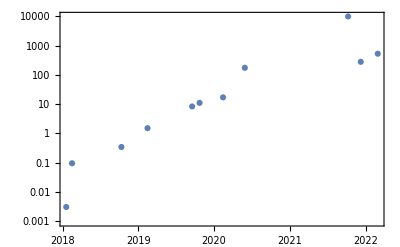

```mathematica
DateListLogPlot[logdata, PlotRange->All,PlotMarkers->Automatic,Joined->False]
```

```mathematica
labeledlogdata=Table[
	Labeled[
		logdata[[i]],Text[Style[annotations[[i]],Bold,14]]],{i,1,Length[logdata]}]
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.003}Ulmfit 3M,{Thu 15 Feb 2018 00:00:00GMT+2,0.094}ELMO 94M,{Thu 11 Oct 2018 00:00:00GMT+2,0.34}BERT 340M,{Thu 14 Feb 2019 00:00:00GMT+2,1.5}GPT2 2B,{Tue 17 Sep 2019 00:00:00GMT+2,8.3}Megatron-LM 8B,{Wed 23 Oct 2019 00:00:00GMT+2,11.}T5 11B,{Thu 28 May 2020 00:00:00GMT+2,175.}GPT3 175B,{Thu 13 Feb 2020 00:00:00GMT+2,17.}Turing-NLG 17B,{Mon 28 Feb 2022 00:00:00GMT+2,530.}Megatron-Turing NLG 530B,{Wed 8 Dec 2021 00:00:00GMT+2,280.}Gopher 280B,{Fri 8 Oct 2021 00:00:00GMT+2,10000.}M6-10T 10000B}

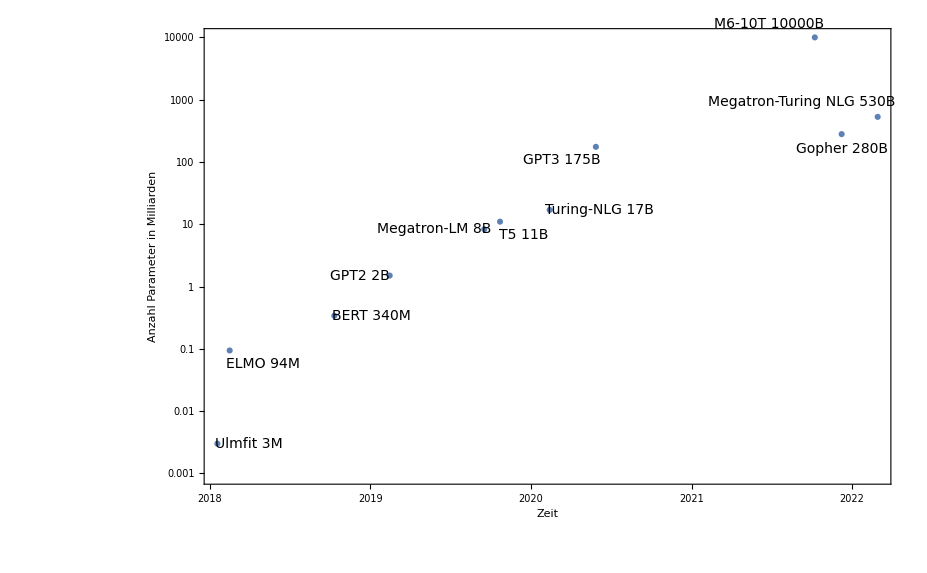

```mathematica
p1=DateListLogPlot[labeledlogdata, 
	PlotRange->All,
	PlotMarkers->Automatic,
	Joined->False,
	FrameLabel->{{Text[Style["Anzahl Parameter in Milliarden",Bold,12]],None},{Text[Style["Zeit",Bold,14]],None}},
	LabelStyle-> Directive[Black, 14]]
```

```mathematica
absdata={AbsoluteTime[#[[1]]],Log10[#[[2]]]}&/@logdata
```

{{3725222400,-2.52288},{3727641600,-1.02687},{3748204800,-0.468521},{3759091200,0.176091},{3777667200,0.919078},{3780777600,1.04139},{3799612800,2.24304},{3790540800,1.23045},{3854995200,2.72428},{3847910400,2.44716},{3842640000,4.}}

```mathematica
timedata=absdata[[All,1]]
```

{3725222400,3727641600,3748204800,3759091200,3777667200,3780777600,3799612800,3790540800,3854995200,3847910400,3842640000}

```mathematica
mint=Min[absdata[[All,1]]];maxt=Max[absdata[[All,1]]];
```

```mathematica
lm=LinearModelFit[absdata,x,x]//Normal
```

-142.184+3.78061×10^-8 x

```mathematica
lmf=Function[y,lm/. x->y]
```

Function[y,lm/.x→y]

```mathematica
regline={DateObject/@timedata,Power[10,lmf/@ timedata]}//Transpose
```

{{Thu 18 Jan 2018 00:00:00GMT+2,0.0448919},{Thu 15 Feb 2018 00:00:00GMT+2,0.0554151},{Thu 11 Oct 2018 00:00:00GMT+2,0.331928},{Thu 14 Feb 2019 00:00:00GMT+2,0.85628},{Tue 17 Sep 2019 00:00:00GMT+2,4.31422},{Wed 23 Oct 2019 00:00:00GMT+2,5.65581},{Thu 28 May 2020 00:00:00GMT+2,29.1461},{Thu 13 Feb 2020 00:00:00GMT+2,13.2313},{Mon 28 Feb 2022 00:00:00GMT+2,3617.22},{Wed 8 Dec 2021 00:00:00GMT+2,1952.21},{Fri 8 Oct 2021 00:00:00GMT+2,1233.88}}

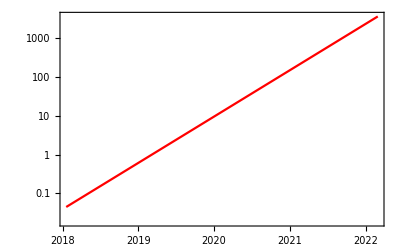

```mathematica
regplot=DateListLogPlot[regline,PlotStyle->Red]
```

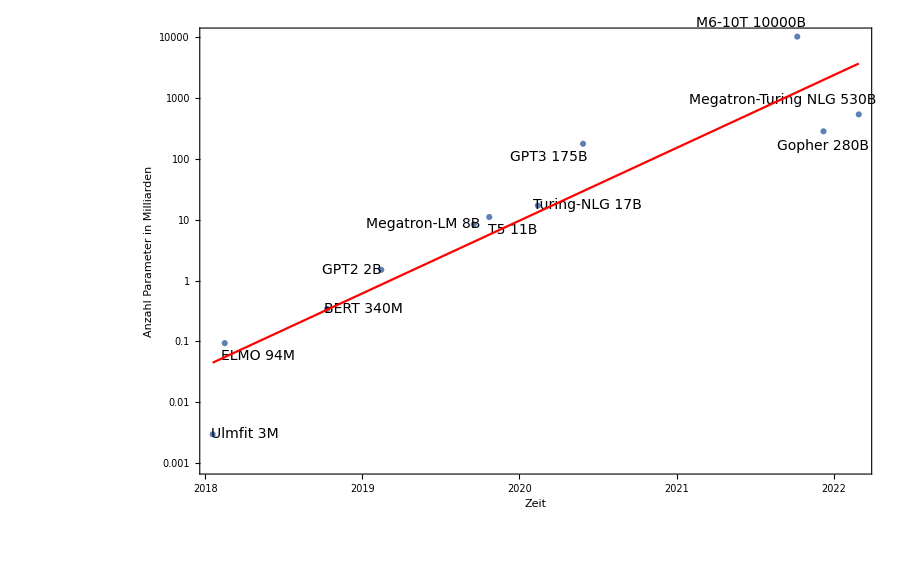

```mathematica
Show[p1,regplot]
```